```mathematica
<<mf23.m
```

```mathematica
cRaleigh2[α_,β_,ν_]:=Module[{answer,pchhmrA,pchhmrB},
pchhmrA=Pochhammer[α,ν];
pchhmrB=Pochhammer[β,ν];
answer=pchhmrA*pchhmrB/(ν!)^2;
Return[answer]]
```

```mathematica
eRaleigh[α_,β_,ν_]:=Sum[1/(α+p)+1/(β+p)-2/(1+p),{p,0,ν-1}]
```

```mathematica
Fraleigh2[α_,β_,u_,terms_]:=Sum[cRaleigh2[α,β,ν]*u^ν,{ν,0,terms}]
```

```mathematica
FstarRaleigh2[α_,β_,u_,terms_]:=
Module[{ν,fsr},
fsr=Sum[cRaleigh2[α,β,ν]*eRaleigh[α,β,ν]*u^ν,{ν,1,terms}];
Return[fsr]]
```

```mathematica
FstarRaleigh3[n_,m_,x_]:=
Module[{α,β,fsr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fsr2=FstarRaleigh2[α,β,x,n];
fsr2=Series[fsr2,{x,0,n}];
Return[fsr2]]
```

```mathematica
Fraleigh4[n_,m_,x_]:=
Module[{α,β,fr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fr2=Fraleigh2[α,β,x,n];
fr2=Series[fr2,{x,0,n}];
Return[fr2]]
```

```mathematica
exNo3[n_,m_,J_]:=
Module[{a1,a2,a3,a4},
a1=J*Exp[FstarRaleigh3[n,m,J]/Fraleigh4[n,m,J]];
a2=Series[a1,{J,0,n}];
a3=Collect[Normal[a2],J];
a4=Series[a3,{J,0,n}];
Return[a4]]
```

```mathematica
J[n_,m_]:=1/InverseSeries[exNo3[n,m,x],x]
```

```mathematica
weight4mDeltaInfty[n_,m_,x_]:=
Module[{jay,djay,numerator,denominator,answer,cl,lcl,notzero,leadingterm,dd,sm,poly},
jay=J[n+1,m];
djay=x*D[jay,x];
numerator=djay^(2*m);
denominator=jay^(2*m-2)*(jay-1)^m;
poly=Collect[Series[(numerator/denominator),{x,0,n}],x];
cl=CoefficientList[poly,x];
dd=Exponent[poly,x];
answer=Sum[cl[[kk]]*x^(kk-1),{kk,1,dd+1}];
lcl=Length[cl];
notzero={};
For[k=0,k<lcl,k++;
If[cl[[k]]!=0,AppendTo[notzero,cl[[k]] ]]];
leadingterm=notzero[[1]];
answer=Collect[answer/leadingterm,x];
Return[answer]];

normalizedWeight4mDeltaInfty[n_,m_,x_]:=
Collect[weight4mDeltaInfty[n+m-2,m,x]/x^(m-2),x];


weight4mDeltaInftyStrike[n_,m_,x_]:=Module[{jay,djay,numerator,denominator,answer,cl,lcl,notzero,leadingterm,dd,sm,poly},

jay=J[n+1,m];
djay=x*D[jay,x];
numerator=djay^(2*m);
denominator=jay^(2*m-2)*(jay-1)^m;
poly=Collect[Series[(numerator/denominator),{x,0,n}],x];
cl=CoefficientList[poly,x];
dd=Exponent[poly,x];
answer=Sum[cl[[kk]]*x^(kk-1),{kk,1,dd+1}];
lcl=Length[cl];
notzero={};
For[k=0,k<lcl,k++;
If[cl[[k]]!=0,AppendTo[notzero,cl[[k]] ]]];
leadingterm=notzero[[1]];
answer=Collect[answer/leadingterm/.x->(2^6*m^3*x),x];
answer=Expand[answer/(2^6*m^3*x)];
Return[answer]];


normalizedWeight4mDeltaInftyStrike[n_,m_,x_]:=
Module[{nw,strike},
nw=normalizedWeight4mDeltaInfty[n,m,x];
strike=nw/.x->(2^6*m^3*x);
Return[strike]]
```

```mathematica
f=x+x^2+5*x^3;
cl=CoefficientList[f,x];
Print[cl];
Print[cl[[4]]]
Print[f/.x->4]
```

{0,1,1,5}

5

340

#### Below matches sagmath ‘conjecture 6.2’

```mathematica
For[m=2,m<6,m++;
Print["-----------------------------------------------------"];
nw=normalizedWeight4mDeltaInfty[5,m,x];
strike=nw/.x->(2^6*m^3*x);
Print[{m,nw}];
Print[{m,strike}];
Print[{m,normalizedWeight4mDeltaInftyStrike[5,m,x]}]]
```

-----------------------------------------------------

{3,1-x/72+(7 x^2)/82944-(23 x^3)/80621568+(805 x^4)/1486016741376-(7 x^5)/17832200896512}

{3,1-24 x+252 x^2-1472 x^3+4830 x^4-6048 x^5}

{3,1-24 x+252 x^2-1472 x^3+4830 x^4-6048 x^5}

-----------------------------------------------------

{4,1-x/16+(11 x^2)/8192-x^3/262144-(325 x^4)/1073741824+(147 x^5)/34359738368}

{4,1-256 x+22528 x^2-262144 x^3-85196800 x^4+4932501504 x^5}

{4,1-256 x+22528 x^2-262144 x^3-85196800 x^4+4932501504 x^5}

-----------------------------------------------------

{5,1-(27 x)/200+(189 x^2)/25600-(3101 x^3)/16000000+(6089013 x^4)/3276800000000+(230691321 x^5)/20480000000000000}

{5,1-1080 x+472500 x^2-99232000 x^3+7611266250 x^4+369106113600 x^5}

{5,1-1080 x+472500 x^2-99232000 x^3+7611266250 x^4+369106113600 x^5}

-----------------------------------------------------

{6,1-(2 x)/9+(7 x^2)/324-(187 x^3)/157464+(901 x^4)/22674816-(7 x^5)/8503056}

{6,1-3072 x+4128768 x^2-3137339392 x^3+1451162075136 x^4-415615395299328 x^5}

{6,1-3072 x+4128768 x^2-3137339392 x^3+1451162075136 x^4-415615395299328 x^5}

```mathematica
fi=normalizedWeight4mDeltaInftyStrike[25,3,x];
ex=Exponent[fi,x];
Print["ex: ",ex];
data={};
For[n=0,n<ex,n++;
cf=Coefficient[fi,x,n];
rt=RamanujanTau[n+1];
AppendTo[data,cf/rt]];
Print[no]
```

ex: 25

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
stream=OpenWrite["run17aug21no80Laptop"]; (* laptop version *)
For[m=2,m<153,m++;
fi=normalizedWeight4mDeltaInftyStrike[50,m,x];
Write[stream,{m,Collect[fi,x]}]];
Close[stream]
```

run17aug21no80Laptop

```mathematica
stream=OpenRead["run17aug21no80Laptop"];
list=ReadList[stream];
Close[stream];
m=Last[list][[1]];
xp=Exponent[Last[list][[2]],x];
Print[{Length[list],m,xp}]
```

{151,153,50}

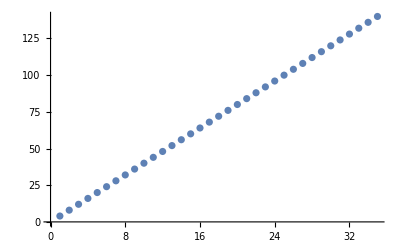

run17aug21no90Laptop

```mathematica
stream=OpenRead["run17aug21no80Laptop"];
list=ReadList[stream];
Close[stream];
wstream=OpenWrite["run17aug21no90Laptop"]; 
degrees={};
For[n=0,n<35,n++;
data={};
For[k=0,k<151,k++;
m=list[[k,1]];
poly=list[[k,2]];
cf=Coefficient[poly,x,n];
AppendTo[data,{m,cf}]
]; (* k *)
ip=InterpolatingPolynomial[data,x];
Write[wstream,{n,ip}];
AppendTo[degrees,{n,Exponent[ip,x]}]
]; (* n *)
Print[ListPlot[degrees]];
Close[wstream]
```

```mathematica
stream=OpenRead["run17aug21no90Laptop"];
list=ReadList[stream];
Close[stream];
Print[Length[list]]
```

35

```mathematica
sstream=OpenRead["run17aug21no90Laptop"];
list=ReadList[stream];
Close[stream];
For[k=0,k<5,k++;
n=list[[k,1]];
poly=list[[k,2]];
poly=Collect[poly,x];
Print["------------------------------------------------------------"];
Print[poly];
poly=factorIntoMonics[poly];
Print[{k,n,poly}]]
```

------------------------------------------------------------

64 x-96 x^2+48 x^3-8 x^4

{1,1,{-8,-8+12 x-6 x^2+x^3,x}}

------------------------------------------------------------

640 x^2-3648 x^3+6080 x^4-4704 x^5+1896 x^6-388 x^7+32 x^8

{2,2,{32,-8+12 x-6 x^2+x^3,x^2,-5/2+(21 x)/2-(49 x^2)/8+x^3}}

------------------------------------------------------------

-(69632 x^3)/27+(354304 x^4)/27+(1254400 x^5)/27-(4556288 x^6)/27+(5641984 x^7)/27-(3711104 x^8)/27+53312 x^9-(36896 x^10)/3+1568 x^11-(256 x^12)/3

{3,3,{-256/3,-8+12 x-6 x^2+x^3,x^3,-34/9+(122 x)/9+(821 x^2)/9-121 x^3+(463 x^4)/8-(99 x^5)/8+x^6}}

------------------------------------------------------------

(1006592 x^4)/27-(9440768 x^5)/27-(23606272 x^6)/27+(22569472 x^7)/9-(6324352 x^8)/9-(8877376 x^9)/3+(112869952 x^10)/27-(75210400 x^11)/27+(30231964 x^12)/27-(859390 x^13)/3+(137752 x^14)/3-4224 x^15+(512 x^16)/3

{4,4,{512/3,-8+12 x-6 x^2+x^3,x^4,-983/36+(7745 x)/36+(141631 x^2)/144-(37883 x^3)/72-(567545 x^4)/576+(695177 x^5)/576-(148023 x^6)/256+(9251 x^7)/64-(75 x^8)/4+x^9}}

------------------------------------------------------------

-(83460096 x^5)/125+(38150291456 x^6)/3375+(5692694528 x^7)/225-(14127509504 x^8)/225-(1695162368 x^9)/125+(123240994816 x^10)/1125-(57475032064 x^11)/675-(3498971648 x^12)/675+(171133817728 x^13)/3375-(137587181504 x^14)/3375+(488050784 x^15)/27-(696703376 x^16)/135+(2929904 x^17)/3-(357568 x^18)/3+(25600 x^19)/3-(4096 x^20)/15

{5,5,{-4096/15,-8+12 x-6 x^2+x^3,x^5,-7641/25+(1061101 x)/225+(1416379 x^2)/75-(99753 x^3)/25-(46381211 x^4)/1800+(10109461 x^5)/600+(18441509 x^6)/3600-(1518721 x^7)/144+(13030631 x^8)/2304-(416675 x^9)/256+(17471 x^10)/64-(101 x^11)/4+x^12}}

--------------------------------------------------------------

n:  1

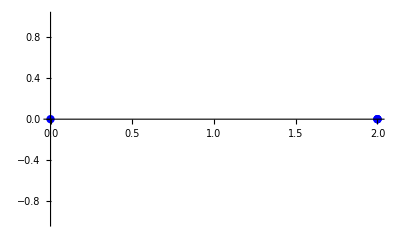

--------------------------------------------------------------

n:  2

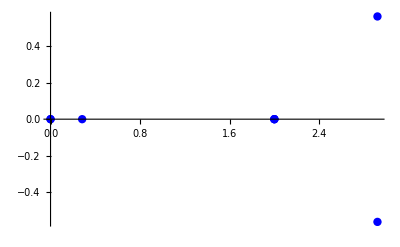

--------------------------------------------------------------

n:  3

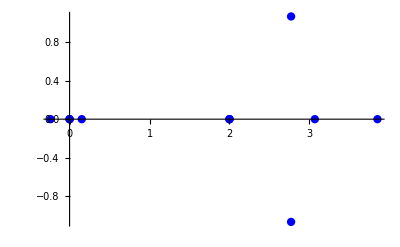

--------------------------------------------------------------

n:  4

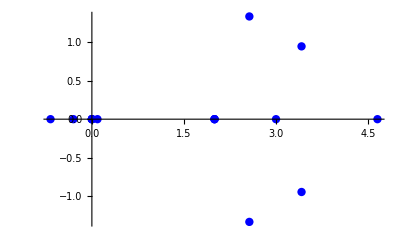

--------------------------------------------------------------

n:  5

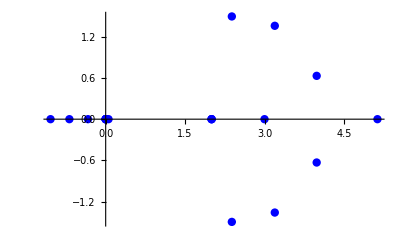

--------------------------------------------------------------

n:  6

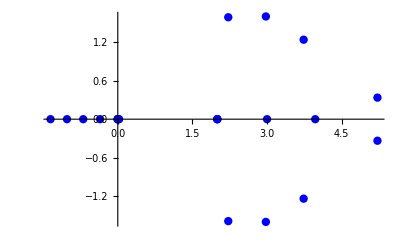

--------------------------------------------------------------

n:  7

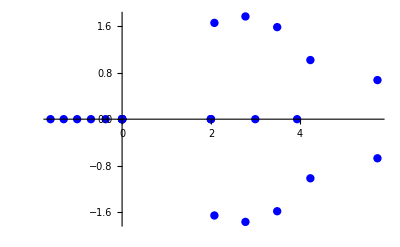

--------------------------------------------------------------

n:  8

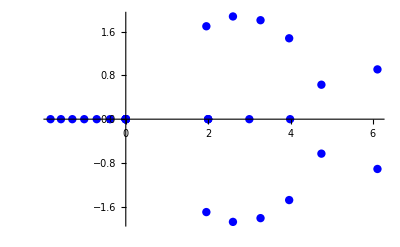

--------------------------------------------------------------

n:  9

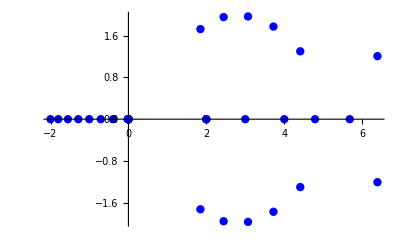

--------------------------------------------------------------

n:  10

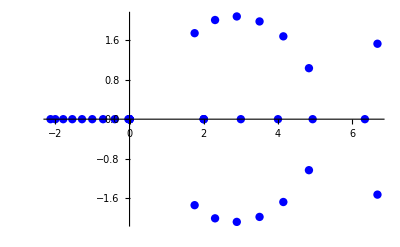

--------------------------------------------------------------

n:  11

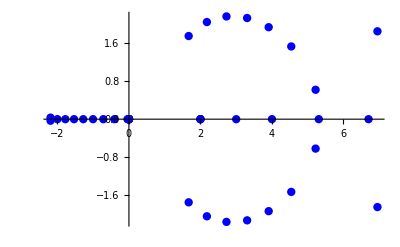

--------------------------------------------------------------

n:  12

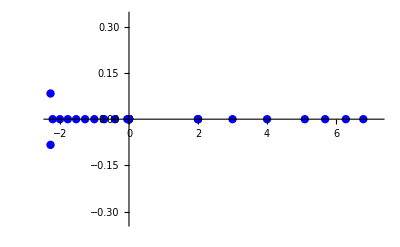

--------------------------------------------------------------

n:  13

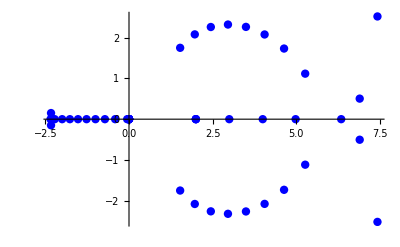

--------------------------------------------------------------

n:  14

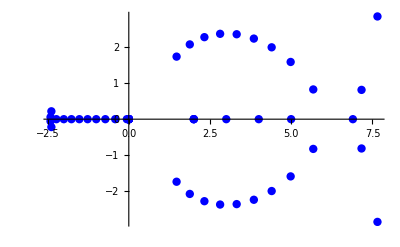

--------------------------------------------------------------

n:  15

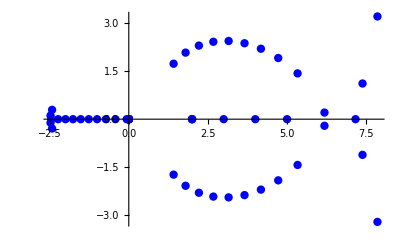

--------------------------------------------------------------

n:  16

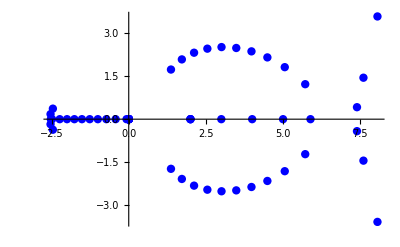

--------------------------------------------------------------

n:  17

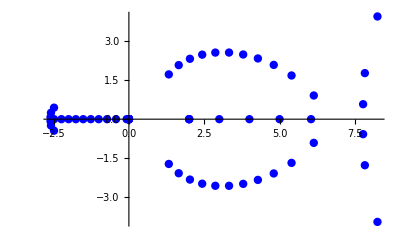

--------------------------------------------------------------

n:  18

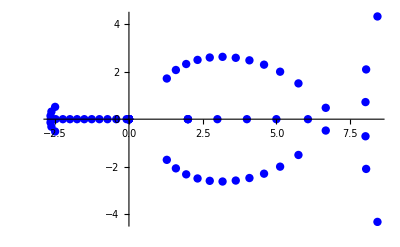

--------------------------------------------------------------

n:  19

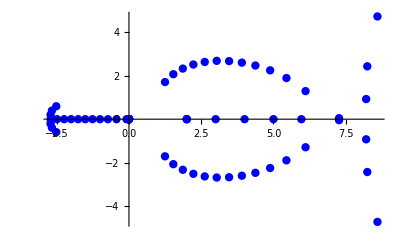

--------------------------------------------------------------

n:  20

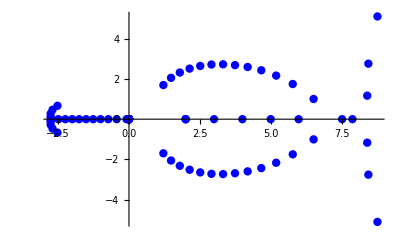

--------------------------------------------------------------

n:  21

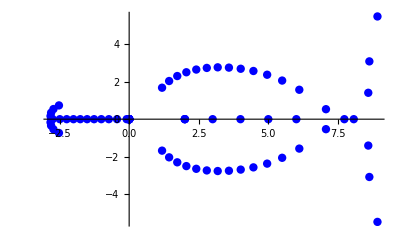

--------------------------------------------------------------

n:  22

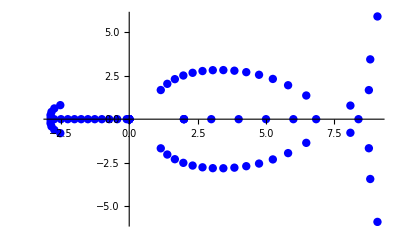

--------------------------------------------------------------

n:  23

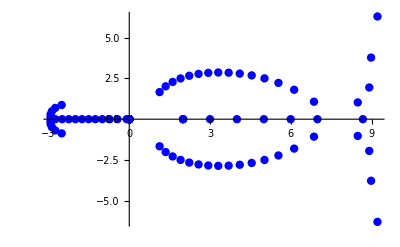

--------------------------------------------------------------

n:  24

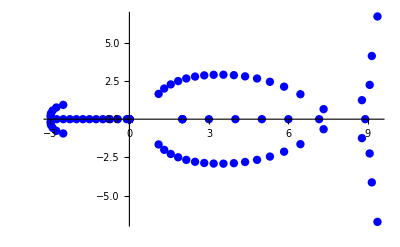

--------------------------------------------------------------

n:  25

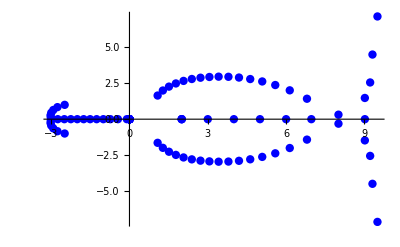

--------------------------------------------------------------

n:  26

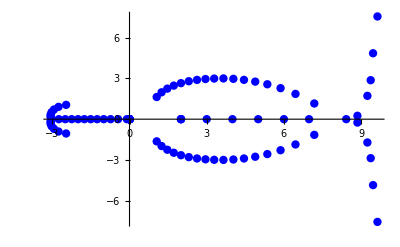

--------------------------------------------------------------

n:  27

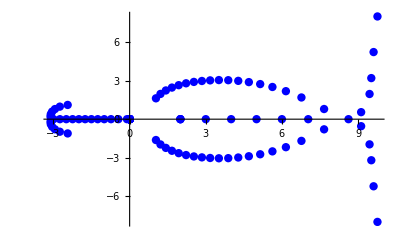

--------------------------------------------------------------

n:  28

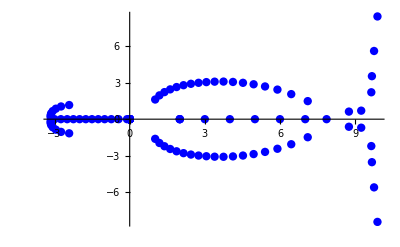

--------------------------------------------------------------

n:  29

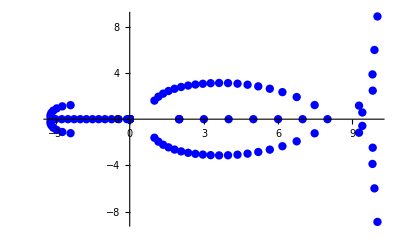

--------------------------------------------------------------

n:  30

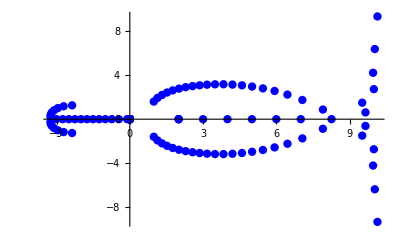

--------------------------------------------------------------

n:  31

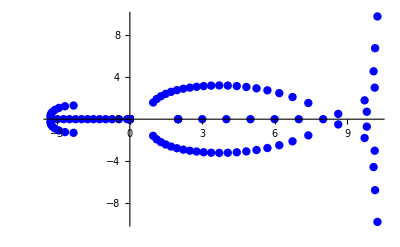

--------------------------------------------------------------

n:  32

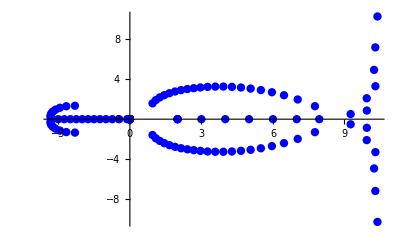

--------------------------------------------------------------

n:  33

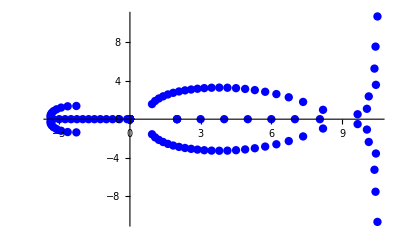

--------------------------------------------------------------

n:  34

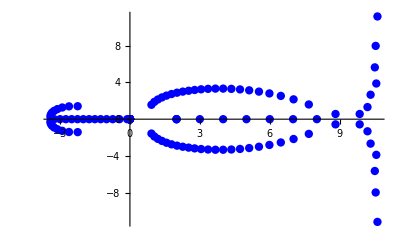

--------------------------------------------------------------

n:  35

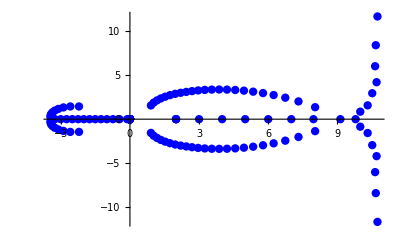

mins

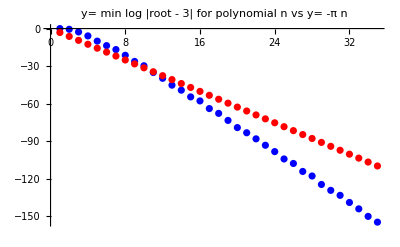

```mathematica
stream=OpenRead["run17aug21no90Laptop"];
list=ReadList[stream];
Close[stream];
pointsize=.015;
color=Blue;
mins={};
degrees={};
no=0;
precision=300;
data={};
For[k=0,k<35,k++;
Print["--------------------------------------------------------------"];
n=list[[k,1]];
poly=list[[k,2]];
Print["n:  ",n];
plotRoots2[poly,x,pointsize,color];
roots=listRoots3[poly,x,precision];
If[MemberQ[roots,3]==True,no++];
min=Min[Log[Abs[roots-3]]];
AppendTo[mins,{n,min}];
AppendTo[data,{n,-Pi*n}]
];
Print["mins"];
lpm=ListPlot[mins,PlotStyle->Blue,PlotLabel->"y= min log |root - 3| for polynomial n vs y= -π n"];
lpd=ListPlot[data,PlotStyle->Red];
Print[Show[lpm,lpd]]
```

--------------------------------------------------------------

n:  1

-Graphics-

--------------------------------------------------------------

n:  2

-Graphics-

--------------------------------------------------------------

n:  3

-Graphics-

--------------------------------------------------------------

n:  4

-Graphics-

--------------------------------------------------------------

n:  5

-Graphics-

--------------------------------------------------------------

n:  6

-Graphics-

--------------------------------------------------------------

n:  7

-Graphics-

--------------------------------------------------------------

n:  8

-Graphics-

--------------------------------------------------------------

n:  9

-Graphics-

--------------------------------------------------------------

n:  10

-Graphics-

--------------------------------------------------------------

n:  11

-Graphics-

--------------------------------------------------------------

n:  12

-Graphics-

--------------------------------------------------------------

n:  13

-Graphics-

--------------------------------------------------------------

n:  14

-Graphics-

--------------------------------------------------------------

n:  15

-Graphics-

--------------------------------------------------------------

n:  16

-Graphics-

--------------------------------------------------------------

n:  17

-Graphics-

--------------------------------------------------------------

n:  18

-Graphics-

--------------------------------------------------------------

n:  19

-Graphics-

--------------------------------------------------------------

n:  20

-Graphics-

--------------------------------------------------------------

n:  21

-Graphics-

--------------------------------------------------------------

n:  22

-Graphics-

--------------------------------------------------------------

n:  23

-Graphics-

--------------------------------------------------------------

n:  24

-Graphics-

--------------------------------------------------------------

n:  25

-Graphics-

--------------------------------------------------------------

n:  26

-Graphics-

--------------------------------------------------------------

n:  27

-Graphics-

--------------------------------------------------------------

n:  28

-Graphics-

--------------------------------------------------------------

n:  29

-Graphics-

--------------------------------------------------------------

n:  30

-Graphics-

--------------------------------------------------------------

n:  31

-Graphics-

--------------------------------------------------------------

n:  32

-Graphics-

--------------------------------------------------------------

n:  33

-Graphics-

--------------------------------------------------------------

n:  34

-Graphics-

--------------------------------------------------------------

n:  35

-Graphics-

mins

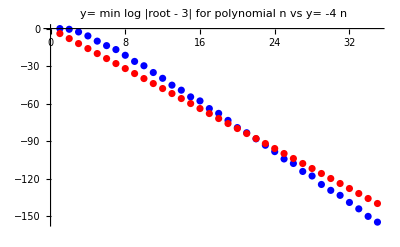

```mathematica
stream=OpenRead["run17aug21no90Laptop"];
list=ReadList[stream];
Close[stream];
pointsize=.015;
color=Blue;
mins={};
degrees={};
no=0;
precision=300;
data={};
For[k=0,k<35,k++;
Print["--------------------------------------------------------------"];
n=list[[k,1]];
poly=list[[k,2]];
Print["n:  ",n];
plotRoots2[poly,x,pointsize,color];
roots=listRoots3[poly,x,precision];
If[MemberQ[roots,3]==True,no++];
min=Min[Log[Abs[roots-3]]];
AppendTo[mins,{n,min}];
AppendTo[data,{n,-4*n}]
];
Print["mins"];
lpm=ListPlot[mins,PlotStyle->Blue,PlotLabel->"y= min log |root - 3| for polynomial n vs y= -4 n"];
lpd=ListPlot[data,PlotStyle->Red];
Print[Show[lpm,lpd]]
```